# Examples of automatic Units package

```mathematica
<<Units`
```

Units replicates the built in Units` package.

```mathematica
Convert[10 Meter, Inch]
```

393.701 Inch

But also automatically coerces compatible units, allowing immediate arithmetic

```mathematica
10 Meter+Inch
```

10.0254 Meter

There is a full form structure that can be used  too

```mathematica
FullForm[%]
```

Unit[10.0254,"Meter"]

Automation works for composite units too

```mathematica
Atmosphere Acre+2 Giga PoundForce
```

9.30649×10^9 Newton

You can also simplify composite units

```mathematica
Simplify[Atmosphere Acre]
```

4.10049×10^8 Newton

Units can be converted to alternative unit sets

```mathematica
Convert[Meter,"Traditional"]
```

1.09361 Yard

Where target unit sets contain multiple choices of the same unit-dimension, the one with the nearest scale is chosem

```mathematica
Convert[2000Meter,"Traditional"]
```

1.24274 Mile

Incompatibility is handled

```mathematica
Day + Inch
```

Unit::incomp1: Units DayInch are not compatible

Day+Inch

Temperatures origins are ignored for standard unit conversion

```mathematica
Celsius/Meter+Fahrenheit/Meter
```

14/9 Kelvin/Meter

But their different origins are respected under ConvertTemperature

```mathematica
ConvertTemperature[0 Celsius,Fahrenheit]
```

32. Fahrenheit

Lots of other operators handle units....inequalities

```mathematica
2000 Meter>1.2 Mile
```

True

Sorting...

```mathematica
Sort[{Foot, Inch, Mile, 200 Yard}]
```

{Inch,Foot,200 Yard,Mile}

Random functions (specific distributions are not yet supported)

```mathematica
RandomReal[{Yard,Meter},{10}]
```

{0.967097 Meter,0.94199 Meter,0.964299 Meter,0.975732 Meter,0.960271 Meter,0.959572 Meter,0.980957 Meter,0.990393 Meter,0.985592 Meter,0.995174 Meter}

Range

```mathematica
Range[10 Meter]
```

{Meter,2 Meter,3 Meter,4 Meter,5 Meter,6 Meter,7 Meter,8 Meter,9 Meter,10 Meter}

```mathematica
Range[10 Meter, 13 Yard, Foot]
```

{10. Meter,10.3048 Meter,10.6096 Meter,10.9144 Meter,11.2192 Meter,11.524 Meter,11.8288 Meter}

As a result of this support some higher operators work too...

```mathematica
Solve[30 x+200 Meter==100Foot,x]
```

{{x→-5.65067 Meter}}

```mathematica
Reduce[30 x+200 Meter==100Foot,x]
```

x==-5.65067 Meter

Plots convert data to common units and display the choice as axes labels

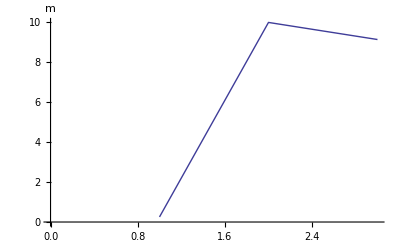

```mathematica
ListLinePlot[{10 Inch,10 Meter,10 Yard}]
```

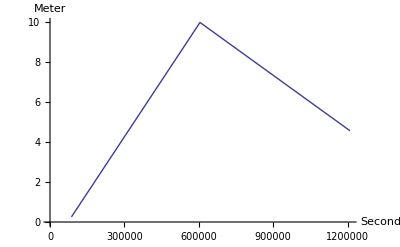

```mathematica
ListLinePlot[{{Day,10 Inch},{Week,10 Meter},{2 Week,5 Yard}}]
```

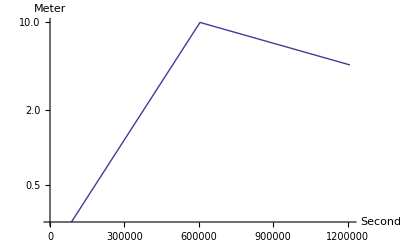

```mathematica
ListLogPlot[{{Day,10 Inch},{Week,10 Meter},{2 Week,5 Yard}},Joined->True]
```

New units can be declared by the user

```mathematica
DeclareUnit["word",Unit[1,"word"]];
DeclareUnit["page",2000 word];
DeclareUnit["book",200 page];
book +200 word
```

400200 word

```mathematica
Convert[book +2000 word, page]
```

201 page

Obscure unit systems are supported...

```mathematica
Convert[1000000 Meter,"Russian"]
```

133.912 Milia

```mathematica
data=Transpose[{
RandomReal[3 Meter,{20}],
RandomReal[3 Week,{20}],
RandomReal[3 Farad,{20}]}];
ListPlot3D[data]
```

-Graphics3D-

```mathematica
data=Transpose[{
RandomReal[3 ,{20}],
RandomReal[3 Week,{20}],
RandomReal[3 Farad,{20}]}];
ListPlot3D[data]
```

-Graphics3D-

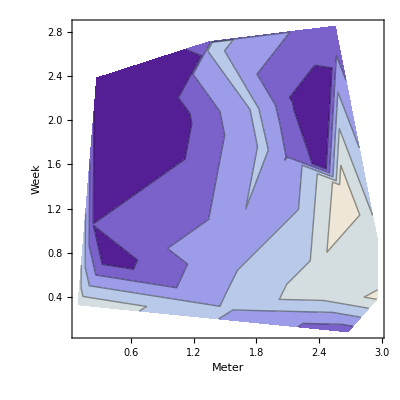

```mathematica
data=Transpose[{
RandomReal[3 Meter,{20}],
RandomReal[3 Week,{20}],
RandomReal[3 Farad,{20}]}];
ListContourPlot[data]
```

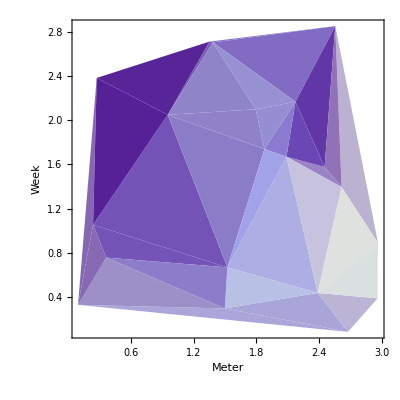

```mathematica
ListDensityPlot[data]
```

```mathematica
2
```

2

```mathematica
data=Transpose[{
RandomReal[{3 Inch ,2 Yard},{20}],
RandomReal[3 Week,{20}],
RandomReal[3 Farad,{20}]}];
ListPointPlot3D[data]
```

-Graphics3D-

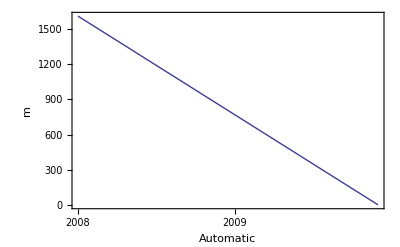

```mathematica
DateListPlot[{{"1 Jan 2008",Mile},{"1 Dec 2009",Meter}},Joined->True]
```

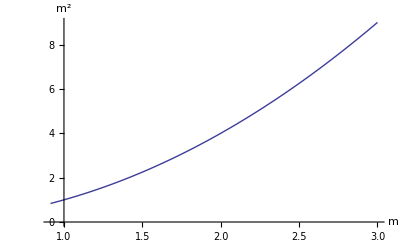

```mathematica
Plot[x^2,{x,3 Foot, 3 Meter}]
```

```mathematica
Plot3D[x^2+y^2,{x,1 Foot, 3Foot},{y,0 Meter, 3 Meter}]
```

-Graphics3D-

```mathematica
Plot3D[(x^2+y^2)/(2 Acre),{x,1 Foot, 3Foot},{y,0 Meter, 3 Meter}]
```

-Graphics3D-

Units have traditional notation with tooltips.

```mathematica
TraditionalForm[Convert[Newton, Atmosphere  Meter^2]]
```

9.86923×10^-6 atm m^2

The standard PhysicalConstants package is compatible

```mathematica
<<PhysicalConstants`
```

EarthMass::shdw: Symbol EarthMass appears in multiple contexts PhysicalConstants`Units`; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

EarthRadius::shdw: Symbol EarthRadius appears in multiple contexts PhysicalConstants`Units`; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

```mathematica
SI[(4 Kilogram √π BoltzmannConstant 300 Kelvin ((BoltzmannConstant 300 Kelvin ProtonMass 2 π PlanckConstantReduced^2)/((PlanckConstant SpeedOfLight) (BoltzmannConstant 300 Kelvin ProtonMass^2)))^(3/2))/(2 PlanckConstant (√((22 29 12)/Centimeter^3) (Meter^2 Second)))]
```

7.72395×10^-16 Newton